# Math 223: Homework 1

<Zihan Xu>

<2/3/2023>

## Problem 1

Use the Series command to compute the Taylor series of (1+x)^(1/x) about x=0. Explore different parameter values to make sure you understand how to use this command. Use the Plot command to plot a comparison of this function with the polynomial of degree 4 given by the partial sum of the Taylor series over the interval [-1,4].

```mathematica
Series[(1+x)^(1/x),{x, 0, 4}]
```

ⅇ-(ⅇ x)/2+(11 ⅇ x^2)/24-(7 ⅇ x^3)/16+(2447 ⅇ x^4)/5760+O[x]^5

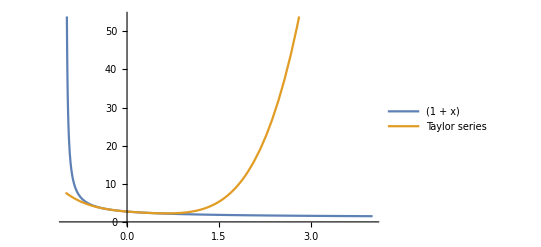

```mathematica
Plot[{(1+x)^(1/x),Evaluate[Normal[Series[(1+x)^(1/x),{x, 0, 4}] ]]}, {x,-1,4},PlotLegends->{"(1 + x)","Taylor series"}]
```

## Problem 2

Use the Integrate command to compute ∫_0^(3/2) sin(x^2)ⅆx. Then use Series within Integrate to integrate the polynomial of degree 6 given by the partial sum of the Taylor series of sin(x^2) about x=0. Use the N command to compute the absolute error made by this approximation.

```mathematica
I1 = Integrate[Sin[x^2],{x,0,3/2}]
```

√(π/2) FresnelS[3/(√(2 π))]

```mathematica
Series[Sin[x^2],{x, 0, 6}]
```

x^2-x^6/6+O[x]^7

```mathematica
I2 = Integrate[Normal[Series[Sin[x^2],{x, 0, 6}]],{x,0,3/2}]
```

1287/1792

```mathematica
Abs[N[I1 - I2]]
```

0.0600458

## Problem 3

Use the DSolve command to solve the following two-point boundary value problem:

ϵ y''+(1+ϵ) y' + y = 0, 0<x<1 ,  
y(0) = 0
y(1) = ⅇ^-1.

Read the documentation to learn how to plot the solution for different values of 0<ϵ ≤ 1. Comment on how the solution changes with ϵ .

```mathematica
sol = DSolve[{δ y''[x]+(1+δ) y'[x] + y[x] == 0, y[0]==0,y[1]==Exp[-1]}, y[x], {x, 0, 1}]
```

{{y[x]→(ⅇ^(-(-1+x+x δ)/δ) (-ⅇ^x+ⅇ^(x/δ)))/(-ⅇ+ⅇ^(1/δ))}}

From this solution, we can see that sol doesn’t exist if ϵ=1. Instead, when ϵ=1, we have to solve the following problem:
 y''+2 y' + y = 0, 0<x<1 ,  
y(0) = 0
y(1) = ⅇ^-1.

```mathematica
sol1=DSolve[{ y''[x]+2 y'[x] + y[x] == 0, y[0]==0,y[1]==Exp[-1]}, y[x], {x, 0, 1}]
```

{{y[x]→ⅇ^-x x}}

We can determine that  y(x) =  ⅇ^-x x, when  ϵ=1. Define a piecewise function y[x,δ] for 0<δ<=1:

```mathematica
y[x_,δ_]:=Piecewise[{{y[x]/.sol,0<δ<1},{y[x]/.sol1,δ==1}},0<δ<=1]
```

```mathematica
y[x,δ]
```

Piecewise[{{{(ⅇ^(-(-1+x+x δ)/δ) (-ⅇ^x+ⅇ^(x/δ)))/(-ⅇ+ⅇ^(1/δ))}, 0<δ<1}, {{ⅇ^-x x}, δ==1}, {0<δ≤1, True}}]

Now, we’re able to plot the solution for different values of 0<ϵ ≤ 1:

```mathematica
Manipulate[Plot[{y[x,δ]/.δ->ϵ},{x,0,1},PlotStyle-> {Directive[Solid,Thickness[0.01]]},AxesLabel->{Style["x",Italic,18],Style["y(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Exact"}],{ϵ,0.005,1,Appearance->"Labeled"},LabelStyle->Directive[Large]]
```

{0.005,0.1,0.3,0.5,0.7,0.9,1}

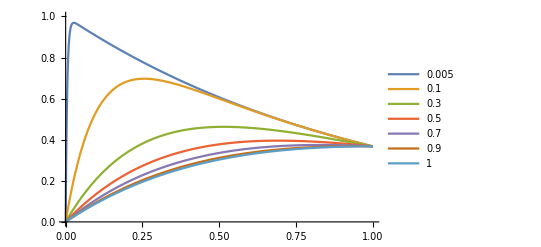

```mathematica
list = {0.005, 0.1, 0.3, 0.5, 0.7, 0.9, 1}
Plot[Evaluate@Table[y[x,δ]/.δ->ϵ,{ϵ,list}],{x,0,1},PlotRange->{0,1}, PlotLegends-> {0.005, 0.1, 0.3, 0.5, 0.7, 0.9, 1}]
```

When ϵ  increases from 0.005 to 1, the graph changes a lot. When ϵ  is close to zero, y(x) increases sharply from 0 to the maximum and then decreases to e^-1 as long as  0<x<1. When ϵ increases from 0 to 1, the maximum decreases until it increases monotonically from 0 to e^-1 as long as  0<x<1. Eventually, the exact solution is ⅇ^-x x when ϵ=1.